```mathematica
SetOptions[EvaluationNotebook[],CellProlog:>SelectionMove[NextCell[CellStyle->"Input"],All,Cell]]
```

```mathematica
U={Us[S,Z,T],Uϕ[S,Z,T],Uz[S,Z,T]};
gradU=Grad[U,{S,Φ,Z},"Cylindrical"];
strainU=gradU+gradUᵀ;
divU=Div[U,{S,Φ,Z},"Cylindrical"];
viscous=ρ0 ν Laplacian[U,{S,Φ,Z},"Cylindrical"];
linearinertia=ρ0(D[U, T]);
nonlinearinertia = ρ0 gradU.U;
pressure=-Grad[P[S,Z,T],{S,Φ,Z},"Cylindrical"];
coriolis=ρ0 Cross[{0,0,2Ω[T]},U];

poincare=ρ0 TransformedField[ "Cartesian"->"Cylindrical",Cross[D[{0,0,Ω[T]},T],{x,y,z}], {x,y,z}->{S,Φ,Z}]//Simplify;
vpmdamping = -ρ0 U/τ;

navierstokes=linearinertia+nonlinearinertia+coriolis+poincare-(pressure+viscous+vpmdamping );
```

```mathematica
EkDef =ν/(H^2 Ω0);
timescale=H/√(ν Ω0)(*H^2/ν*);
velscale=(*ν/H*)Ω0 H;
pressurescale =(* ν ρ0 Ω*)ρ0*velscale^2;
ηDef = τ velscale/H;
nondim={
T->t timescale,
S->H s,
Z-> H z,
Φ->ϕ,
Us->(velscale*us[#1/H,#2/H,#3/timescale]&),
Uϕ->(velscale*uϕ[#1/H,#2/H,#3/timescale]&),
Uz->(velscale *uz[#1/H,#2/H,#3/timescale]&),
P->(pressurescale*p[#1/H,#2/H,#3/timescale]&),
Ω->(Ω0(1 + ΔΩ[#1/timescale])&),
Solve[EkDef==Ek,ν][[1]][[1]],
Solve[ηDef ==η,τ][[1]][[1]]
};
```

```mathematica
ϵDef = √(ν τ)/H;
Assuming[{H>0},FullSimplify[ϵDef ==(ηDef EkDef)^(1/2)]]
```

True

```mathematica
ndimmomentum=Assuming[{H>0,Ω0>0},FullSimplify[H/(ρ0*velscale^2)navierstokes//.nondim//ExpandAll]]//ExpandAll;

ndimmomentumRHS = Assuming[{H>0,Ω0>0},FullSimplify[H/(ρ0*velscale^2)(-nonlinearinertia+vpmdamping)//.nondim//ExpandAll]]//ExpandAll;
ndimmomentumLHS = ndimmomentum+ndimmomentumRHS//FullSimplify
```

{(Ek us[s,z,t])/s^2-2 uϕ[s,z,t] (1+ΔΩ[t])+√Ek us^(0,0,1)[s,z,t]+p^(1,0,0)[s,z,t]-(Ek (us^(1,0,0)[s,z,t]+s (us^(0,2,0)[s,z,t]+us^(2,0,0)[s,z,t])))/s,(Ek uϕ[s,z,t])/s^2+2 us[s,z,t] (1+ΔΩ[t])+√Ek s ΔΩ'[t]+√Ek uϕ^(0,0,1)[s,z,t]-Ek uϕ^(0,2,0)[s,z,t]-(Ek uϕ^(1,0,0)[s,z,t])/s-Ek uϕ^(2,0,0)[s,z,t],√Ek uz^(0,0,1)[s,z,t]+p^(0,1,0)[s,z,t]-(Ek (uz^(1,0,0)[s,z,t]+s (uz^(0,2,0)[s,z,t]+uz^(2,0,0)[s,z,t])))/s}

```mathematica
ndcont=(H s)/velscale divU//.nondim//ExpandAll
```

us[s,z,t]+s uz^(0,1,0)[s,z,t]+s us^(1,0,0)[s,z,t]

```mathematica
dedcleanup={
f_[s,z,t]->f,
g_[t]->g,
Derivative[j_/;j==1,k_,l_][f_]->(ds^j)[Derivative[0,k,l][f]],
Derivative[j_,k_/;k==1,l_][f_]->(dz^k)[Derivative[j,0,l][f]],
Derivative[j_,k_,l_/;l==1][f_]->dt[Derivative[j,k,0][f]],
Derivative[j_/;j>1,k_,l_][f_]->ds[Derivative[j-1,k,l][f]],
Derivative[j_,k_/;k>1,l_][f_]->dz[Derivative[j,k-1,l][f]],
Derivative[j_,k_,l_/;l>1][f_]->dt[Derivative[j,k,l-1][f]],
Derivative[l_/;l==1][g_]->dt[g],
Derivative[l_/;l>1][g_]->dt[Derivative[l-1][g]],
uϕ->uphi,
η->eta,
ΔΩ->DelOmega
};

dedstringcleanup={
"ds(us)"->"ds_us",
"ds(uphi)"->"ds_uphi",
"ds(uz)"->"ds_uz",
"Sqrt"->"np.sqrt",
"dt(DelOmega)"->"dt_DelOmega"
};
```

```mathematica
ndimmomentum[[1]]//.dedcleanup
ndimmomentum[[2]]//.dedcleanup
ndimmomentum[[3]]//.dedcleanup
```

-2 uphi-2 DelOmega uphi-uphi^2/s+us/eta+(Ek us)/s^2+ds[p]-(Ek ds[us])/s+us ds[us]-Ek ds[ds[us]]+√Ek dt[us]+uz dz[us]-Ek dz[dz[us]]

uphi/eta+(Ek uphi)/s^2+2 us+2 DelOmega us+(uphi us)/s-(Ek ds[uphi])/s+us ds[uphi]-Ek ds[ds[uphi]]+√Ek s dt[DelOmega]+√Ek dt[uphi]+uz dz[uphi]-Ek dz[dz[uphi]]

uz/eta-(Ek ds[uz])/s+us ds[uz]-Ek ds[ds[uz]]+√Ek dt[uz]+dz[p]+uz dz[uz]-Ek dz[dz[uz]]

```mathematica
Print[StringReplace[ToString[(s^2 ndimmomentumLHS[[1]]//ExpandAll)//.dedcleanup//FortranForm]<>"="<>ToString[(s^2 ndimmomentumRHS[[1]]//ExpandAll)//.dedcleanup//FortranForm],dedstringcleanup]]
Print[StringReplace[ToString[(s^2 ndimmomentumLHS[[2]]//ExpandAll)//.dedcleanup//FortranForm]<>"="<>ToString[(s^2 ndimmomentumRHS[[2]]//ExpandAll)//.dedcleanup//FortranForm],dedstringcleanup]]
Print[StringReplace[ToString[(s ndimmomentumLHS[[3]]//ExpandAll)//.dedcleanup//FortranForm]<>"="<>ToString[(s ndimmomentumRHS[[3]]//ExpandAll)//.dedcleanup//FortranForm],dedstringcleanup]]
```

-2*s**2*uphi - 2*DelOmega*s**2*uphi + Ek*us + s**2*ds(p) - Ek*s*ds_us - Ek*s**2*ds(ds_us) + np.sqrt(Ek)*s**2*dt(us) - Ek*s**2*dz(dz(us))=s*uphi**2 - (s**2*us)/eta - s**2*us*ds_us - s**2*uz*dz(us)

Ek*uphi + 2*s**2*us + 2*DelOmega*s**2*us - Ek*s*ds_uphi - Ek*s**2*ds(ds_uphi) + np.sqrt(Ek)*s**3*dt_DelOmega + np.sqrt(Ek)*s**2*dt(uphi) - Ek*s**2*dz(dz(uphi))=-((s**2*uphi)/eta) - s*uphi*us - s**2*us*ds_uphi - s**2*uz*dz(uphi)

-(Ek*ds_uz) - Ek*s*ds(ds_uz) + np.sqrt(Ek)*s*dt(uz) + s*dz(p) - Ek*s*dz(dz(uz))=-((s*uz)/eta) - s*us*ds_uz - s*uz*dz(uz)

```mathematica
Print[StringReplace[ToString[ndcont//.dedcleanup//FortranForm],dedstringcleanup]]
```

us + s*ds_us + s*dz(uz)

```mathematica
mask[x_]=0.5*(1+Tanh[-2x])
```

0.5 (1-Tanh[2 x])

```mathematica
Sech[x]
```

Sech[x]

```mathematica
D[Sech[x],x]
```

-Sech[x] Tanh[x]

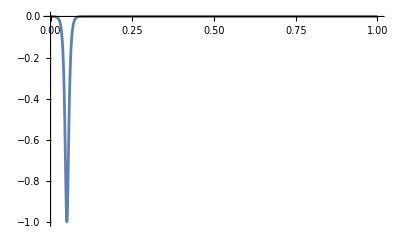

```mathematica
Plot[-Sech[(x-0.05)/0.005],{x,0.,1},PlotRange->All]
```

```mathematica
delOmega[t_,del_]=-1+0.5(1-Tanh[-2 ((t-2*del)/del)])
D[delOmega[t,del],t]//FortranForm
```

-1+0.5 (1+Tanh[(2 (-2 del+t))/del])

(1.*Sech((2*(-2*del + t))/del)**2)/del

0.1

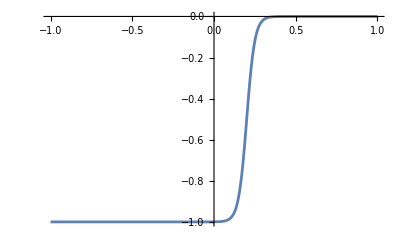

```mathematica
delay=0.1
Plot[delOmega[t,delay],{t,-1,1}]
```

```mathematica
(s^2 ndimmomentum[[1]]//ExpandAll)//.{s->0}
(s^2 ndimmomentum[[2]]//ExpandAll)//.{s->0}
(s ndimmomentum[[3]]//ExpandAll)//.{s->0}
```

Ek us[0,z,t]

Ek uϕ[0,z,t]

-Ek uz^(1,0,0)[0,z,t]

```mathematica
ndcont
```

us[s,z,t]+s uz^(0,1,0)[s,z,t]+s us^(1,0,0)[s,z,t]